```mathematica
<<MaTeX`
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";
plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,plotType]))/.Directive[x_,__]:>x;
pltcolors=plotColors[ListLinePlot,"Scientific"];
```

```mathematica
totald431=10*5000000;
d431pPOT=1.2*10^-6;
ncm2=700*300;
POTpyear=1.47*10^21;
brfactor=1;
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2*brfactor
```

168.

## bg-meta plot

### Data

```mathematica
xmin=0;
xmax=40;
nbins=40;
xrange=N[Table[xmin+i*(xmax-xmin)/nbins,{i,0,nbins}]];
nudata=Import[NotebookDirectory[]<>"meta-1.dat"];
nubardata=Import[NotebookDirectory[]<>"meta-2.dat"];
nutable={};
nubartable={};
Do[
AppendTo[nutable,Table[{xrange[[l]],nudata[[i,l]]*d431factor},{l,1,nbins+1}]];
AppendTo[nubartable,Table[{xrange[[l]],nubardata[[i,l]]*d431factor},{l,1,nbins+1}]];
,{i,1,15*3}]
f[mhnl_,flavour_]:=nutable[[IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]];
fbar[mhnl_,flavour_]:=nubartable[[IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]];
```

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["\\text{off-axis (m)}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
latext1=MaTeX["\\text{mHNL=1.9 GeV}",Magnification->magnificationlegends,ContentPadding->False];
```

### Config Plots

```mathematica
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle={{pltcolors[[1]],Automatic},{pltcolors[[2]],Automatic},{pltcolors[[3]],Automatic},{pltcolors[[1]],Dashed},{pltcolors[[2]],Dashed},{pltcolors[[3]],Dashed}};
imagesize={300,Automatic};
background=White;
yticks=Join[Table[{i*10^5,""},{i,1,9,1}],Table[{i*10^6,""},{i,1,9,1}],Table[{i*10^7,""},{i,1,9,1}],Table[{i*10^8,""},{i,1,9,1}],{{10^6,"10^6"},{10^7,"10^7"},{10^8,"10^8"}}];
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
```

### Plots Nu

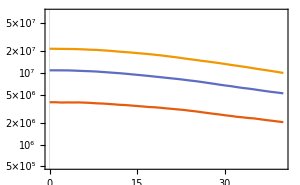

```mathematica
m=1.9;
plotrange={{0,40},{5*10^5,7*10^7}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{f[m,1],f[m,2],f[m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexp=Show[plot1,text]
Export[NotebookDirectory[]<>"meta-"<>ToString[NumberForm[m,{2,1}]]<>".pdf",plotexp];
```

### Plots Nubar

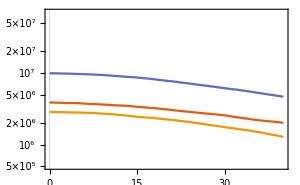

```mathematica
m=1.9;
plotrange={{0,40},{5*10^5,7*10^7}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{fbar[m,1],fbar[m,2],fbar[m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexp=Show[plot1,text]
Export[NotebookDirectory[]<>"metabar-"<>ToString[NumberForm[m,{2,1}]]<>".pdf",plotexp];
```

## Backup

```mathematica
plotid={1,2,3};
tablelegend1=Table[ToString[12+2*(plotid[[i]]-1)],{i,1,Dimensions[plotid][[1]]}];
```

```mathematica
plotid={1,2,3};
tableplot1=Table[nutable[[plotid[[i]]]],{i,1,Dimensions[plotid][[1]]}];
tableplot2=Table[nubartable[[plotid[[i]]]],{i,1,Dimensions[plotid][[1]]}];
tableplot=Join[tableplot1,tableplot2];
```

# sdasd

```mathematica
asda
```

```mathematica
asdasd
```